```mathematica
c = (1/3)(1-1/(1+Tanh[k Log[1/a0]]));
b = ((-1)/3)(1/(1+Tanh[k Log[1/a0]]));
Simplify[b Log[a0]]
f[a_]:= c+b Tanh[k Log[a/a0]];
mtoa0[m_]:=1/(1+1890 m);
```

-(Log[a0]/(3 (1+Tanh[k Log[1/a0]])))

```mathematica
D[f[a],a]
```

-(k Sech[k Log[a/a0]]^2)/(3 a (1+Tanh[k Log[1/a0]]))

```mathematica
mtoa0[0.1]
```

0.00526316

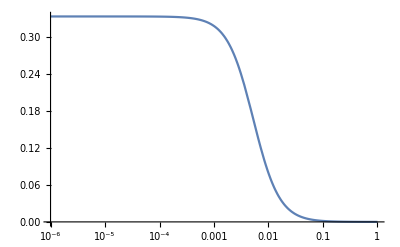

```mathematica
a0 = mtoa0[0.1];
k = 0.90885;
LogLinearPlot[f[a],{a,10^-6,1}]
Clear[a0,k]
```

```mathematica
-3Integrate[1/ap(1+f[ap]),{ap,aini,a}]
```

$Aborted

```mathematica
Clear[c,b]
int = Integrate[(1+c+b Tanh[k up -k Log[a0]]),up]/. up-> Log[a]
```

Log[a]+c Log[a]+(b Log[Cosh[k (Log[a]-Log[a0])]])/k

```mathematica
int/. a-> 1
```

-Log[Cosh[k Log[a0]]]/(3 k (1+Tanh[k Log[1/a0]]))

```mathematica
Limit[int,up-> -∞]
```

ConditionalExpression[-∞, (1/(3+3 Tanh[k Log[1/a0]])|Log[a0]|Tanh[k Log[1/a0]])∈ℝ&&k>0]

```mathematica
Series[1/u+c 1/u+(b Log[Cosh[k (1/u-Log[a0])]])/k,{u,0,2}]
```

(b Log[Cosh[k/u-k Log[a0]+O[u]^3]])/k+((1+c)/u+O[u]^3)

### Toni’s tanh

```mathematica
f[x_]:= 1/6(1-Tanh[k (Log[x/a0])])
```

```mathematica
D[f[x],x]
```

-(k Sech[k Log[x/a0]]^2)/(6 x)

```mathematica
flog[u_]:= 1/6(1-Tanh[k (u - Log[a0])]);
Integrate[1+flog[up],up]
Integrate[1+flog[up],{up,uini,u},Assumptions->{uini>0,u>0,a0>0,k>0}]
```

(7 up)/6-Log[Cosh[k (up-Log[a0])]]/(6 k)

```mathematica
Clear[aini]
int[a_]:=1/6 (7 Log[a/aini]-Log[Cosh[k (Log[a/a0])] Sech[k (Log[aini/a0])]]/k)
```

```mathematica
Limit[Exp[-3int[a]]/aini^4,aini->0]
```

ConditionalExpression[Indeterminate, a>0&&a0>0&&k>0]

```mathematica
Clear[aini];
Integrate[1+f[x]/. k->1,{x,aini,a},Assumptions->{k>0,a0>0,aini>0,a>0}]
```

a-aini+1/3 a0 ArcTan[a/a0]-1/3 a0 ArcTan[aini/a0]

```mathematica
Limit[ArcTan[x],x-> 0]
```

0

```mathematica
Series[Exp[-a0/3 ArcTan[a/a0]],{a,0,2}]
```

1-a/3+a^2/18+O[a]^3

```mathematica
Clear[aini]
a = 4/3 Log[aini]-1/6 Log[a0]+Log[2]/(6k);
FullSimplify[Exp[-3a],Assumptions->{a0>0,aini>0}]
```

(2^(-1/2/k) √a0)/aini^4